```mathematica
(* 用DSolve求解线性以及非线性微分方程通解 *)
DSolve[y'[x]==x^2 Sin[x],y[x],x] (*第二个参数是方程本身，第三个参数是自变量*)
```

{{y[x]→C[1]-(-2+x^2) Cos[x]+2 x Sin[x]}}

```mathematica
DSolve[{y'[x]==x^2 Sin[x],y[1]==1},y[x],x] (*求解微分方程的特解，初始值使用花括号与微分方程一同括起来*)
```

{{y[x]→1-Cos[1]+2 Cos[x]-x^2 Cos[x]-2 Sin[1]+2 x Sin[x]}}

```mathematica
soln = DSolveValue[{y'[x]==x^2 Sin[x],y[1]==1},y[x],x]
```

1-Cos[1]+2 Cos[x]-x^2 Cos[x]-2 Sin[1]+2 x Sin[x]

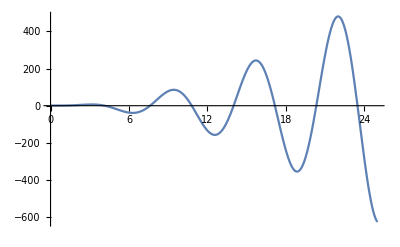

```mathematica
soln = DSolveValue[{y'[x]==x^2 Sin[x],y[1]==1},y[x],x];
(* 可视化微分方程的解 *)
Plot[soln,{x,0,25}]
```

```mathematica
soln = DSolve[{y''[x]+y'[x]+y[x]==0,y[0]==0,y'[1]==1},y[x],x]
```

{{y[x]→(2 ⅇ^(1/2-x/2) Sin[(√3 x)/2])/(√3 Cos[(√3)/2]-Sin[(√3)/2])}}

```mathematica
soln = DSolveValue[{y''[x]+y'[x]+y[x]==0,y[0]==0,y'[1]==1},y[x],x]
```

(2 ⅇ^(1/2-x/2) Sin[(√3 x)/2])/(√3 Cos[(√3)/2]-Sin[(√3)/2])

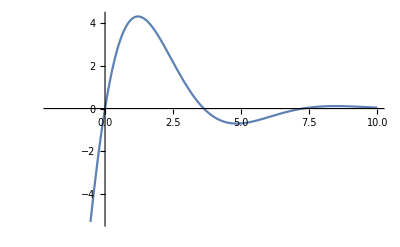

```mathematica
Plot[soln,{x,-2,10}]
```

```mathematica
(* 得到上述方程的通解 *)
soln = DSolveValue[y''[x]+y'[x]+y[x]==0,y[x],x]
```

ⅇ^(-x/2) C[2] Cos[(√3 x)/2]+ⅇ^(-x/2) C[1] Sin[(√3 x)/2]

```mathematica
(* 探索多个特解 *)
solnTable = Table[soln /. {C[2] ->j,C[1] ->i},{i,-1,1,1},{j,-1,1,1}]
```

{{-ⅇ^(-x/2) Cos[(√3 x)/2]-ⅇ^(-x/2) Sin[(√3 x)/2],-ⅇ^(-x/2) Sin[(√3 x)/2],ⅇ^(-x/2) Cos[(√3 x)/2]-ⅇ^(-x/2) Sin[(√3 x)/2]},{-ⅇ^(-x/2) Cos[(√3 x)/2],0,ⅇ^(-x/2) Cos[(√3 x)/2]},{-ⅇ^(-x/2) Cos[(√3 x)/2]+ⅇ^(-x/2) Sin[(√3 x)/2],ⅇ^(-x/2) Sin[(√3 x)/2],ⅇ^(-x/2) Cos[(√3 x)/2]+ⅇ^(-x/2) Sin[(√3 x)/2]}}

```mathematica
TableForm[solnTable]
```

-ⅇ^(-x/2) Cos[(√3 x)/2]-ⅇ^(-x/2) Sin[(√3 x)/2] | -ⅇ^(-x/2) Sin[(√3 x)/2] | ⅇ^(-x/2) Cos[(√3 x)/2]-ⅇ^(-x/2) Sin[(√3 x)/2]
-ⅇ^(-x/2) Cos[(√3 x)/2] | 0 | ⅇ^(-x/2) Cos[(√3 x)/2]
-ⅇ^(-x/2) Cos[(√3 x)/2]+ⅇ^(-x/2) Sin[(√3 x)/2] | ⅇ^(-x/2) Sin[(√3 x)/2] | ⅇ^(-x/2) Cos[(√3 x)/2]+ⅇ^(-x/2) Sin[(√3 x)/2]

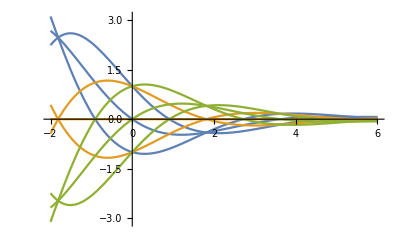

```mathematica
Plot[solnTable,{x,-2,6},PlotRange->All]
```

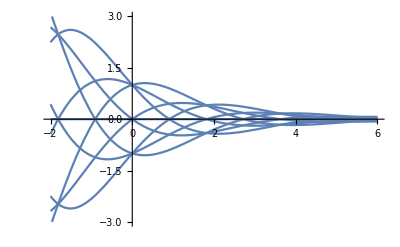

```mathematica
Plot[Table[soln /. {C[2] ->j,C[1]->i },{i,-1,1,1},{j,-1,1,1}],{x,-2,6},PlotRange->{-3,3}]
```

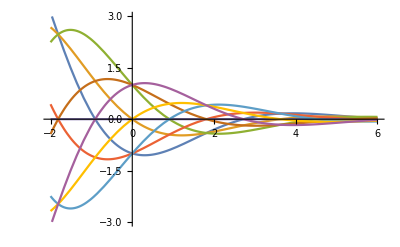

```mathematica
Plot[
	Evaluate[
	Table[
	soln /. {C[2] ->j,C[1]->i },
	{i,-1,1,1},
	{j,-1,1,1}	
 ]
 ],
    {x,-2,6},
    PlotRange->{-3,3}
] (* 如果需要绘制出颜色，需要提前计算方程的实际解 *)
```

```mathematica
Manipulate[
Plot[
	soln /. {C[2] ->j,C[1]->i },
	{x,-2,6},
	PlotRange->{-3,3}
],
{i,-1,1,1},
{j,-1,1,1},
Initialization:>(soln=DSolveValue[{y''[x]+y'[x]+y[x]==0},y[x],x])
]
```

```mathematica
(* 使用NDSolve求解数值解 *)
NDSolveValue[{y'[x]==x^2 Sin[x],y[1]==1},y,{x,0,10}]
```

InterpolatingFunction[…]

```mathematica
nSoln = NDSolveValue[{y'[x]==x^2 Sin[x],y[1]==1},y,{x,0,10}]
```

InterpolatingFunction[…]

```mathematica
nSoln[5]
```

-17.3367

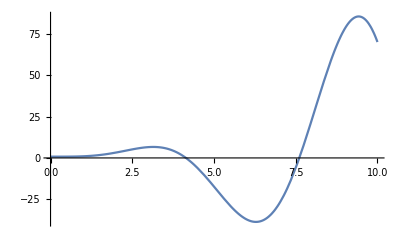

```mathematica
Plot[nSoln[x],{x,0,10}]
```

```mathematica
NIntegrate[nSoln[x],{x,0,10}]
```

72.4684

```mathematica
sysSoln = NDSolveValue[
{x'[t]-4x[t]+y''[t]==t^2/2,x'[t]+2x[t]+2y'[t]==0,x[0]==0,x[1]==1,y[0]==0},
{x[t],y[t]},
{t,0,5}
]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

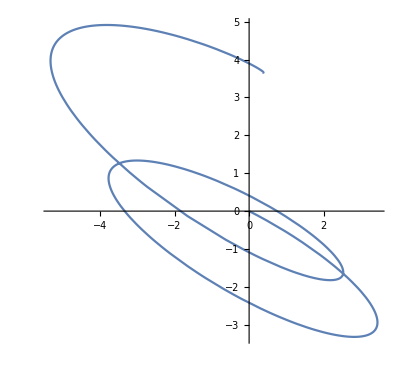

```mathematica
ParametricPlot[sysSoln,{t,0,5}]
```

```mathematica
(* 求解偏微分方程 *)
pdeSoln = NDSolveValue[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u[t,x],{t,0,20},{x,0,5}]
```

InterpolatingFunction[…][t,x]

```mathematica
Plot3D[pdeSoln,{t,0,20},{x,0,5},PlotRange->All,ColorFunction->"DeepSeaColors"]
```

-Graphics3D-

```mathematica
Clear[soln,solnTable,nSoln,sysSoln,pdeSoln]
```